3.78792×10^11 ep

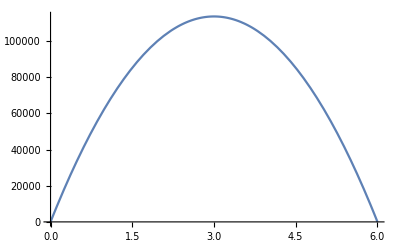

```mathematica
lj93[r_,ξ_,σ_]=-ξ*1.5*3^(1/2)(1/r^5)(-9 σ^9/r^6+σ^3)r;
lj93c[r_,ξ_,σ_]=-3/2 √3 ξ ((3 σ^3)/r^4-(9 σ^9)/r^10);


lj[r_,ξ_,σ_,rc_]:=If[r<rc σ,-4 ξ ((6 σ^6)/r^7-(12 σ^12)/r^13),0];
coulomb[r_,ep_,q_]=1/(4 π ep)q^2/r^2;
imagePot[r_,ep_,q_]=1/(4 π ep)q/r;
L=6 10^-7;
ϵ=586.66 10^-21;
q1=1.6 10^-19;
grad=(ep q1/(2(L)^2 ϵ))
(*eqLow=ϵ D[ϕ[y],{y,2}]==-2q1 /(L^3);
gradLow=(2 q1/(2(L)^2 ϵ));
eqHigh=ϵ D[ϕ[y],{y,2}]==-40q1 /(L^3);
gradHigh=(40 q1/(2(L)^2 ϵ));

esPotentialLow[y_]=NDSolve[{eqLow,ϕ'[0]==gradLow ,ϕ'[L]==-gradLow},ϕ[y],y][[1,1,2]];
esPotentialHigh[y_]=DSolve[{eqHigh,ϕ'[0]==gradHigh ,ϕ'[L]==-gradHigh},ϕ[y],y][[1,1,2]];
Plot[esPotentialLow[y],{y,0,L}]
Plot[esPotentialHigh[y],{y,0,L}]*)
(*eq=ϵ D[ϕ[y],{y,2}]==-ep q /(L^3);
grad=(ep q/(2(L)^2 ϵ));*)
esPot[y_,ep_]=-(ep q1)/(2 L^3 ϵ) (y-L)y;

Plot[esPot[y,2], {y,0,L}]
```

```mathematica
Clear[q1,ϵ,q,L]

Solve[-A L==(ep q1/(2(L)^2 ϵ)),A]
```

{{A→-(ep q1)/(2 L^3 ϵ)}}

```mathematica
D[A (y-L)y,y]/.y->0
```

-A L

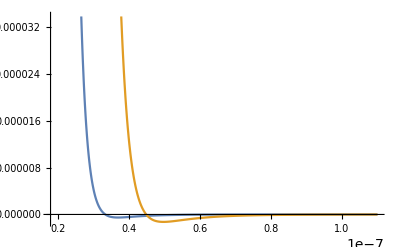

```mathematica
σcs=2.96 10^-8;
ξcs=6.46 10^-15;
rccs=3.72;

σas=3.99 10^-8;
ξas=2.12 10^-14;
rcas=2.84;

Plot[{lj[r,ξcs,σcs,rccs],lj[r,ξas,σas,rcas]},{r,0.6σcs,rccs σcs}]
```

```mathematica
lattice = Import["~/bottomWall.dat"][[2;;-1]];
NL=Length[lattice];
```

```mathematica
NN=200;
NP=250;

ydiv=rccs σcs/NP;
potTabCS={};
For[i=1,i<=NP,i++,
yp=i*ydiv;
potTot=0;
For[j=1,j<=NN,j++,
xp=RandomReal[]*L;
zp=RandomReal[]*L;
pot=0;
For[k=1,k<=NL,k++,
rp=((lattice[[k,1]]-xp)^2+(lattice[[k,2]]-yp)^2+(lattice[[k,3]]-zp)^2)^(1/2);
pot = pot + lj[rp,ξcs,σcs,rccs];
];
potTot = potTot+pot;
];
potTot = potTot/NL;
AppendTo[potTabCS,{yp,potTot}];
];
potFuncCS=Interpolation[potTabCS]
```

InterpolatingFunction[…]

```mathematica
NN=200;
NP=250;
ydiv=5rcas σas/NP;
potTabAS={};
For[i=1,i<=NP,i++,
yp=i*ydiv;
potTot=0;
For[j=1,j<=NN,j++,
xp=RandomReal[]*L;
zp=RandomReal[]*L;
pot=0;
For[k=1,k<=NL,k++,
rp=((lattice[[k,1]]-xp)^2+(lattice[[k,2]]-yp)^2+(lattice[[k,3]]-zp)^2)^(1/2);
pot = pot + lj[rp,ξas,σas,rcas];
];
potTot = potTot+pot;
];
potTot = potTot/NL;
AppendTo[potTabAS,{yp,potTot}];
];
potFuncAS=Interpolation[potTabAS]
```

InterpolatingFunction[…]

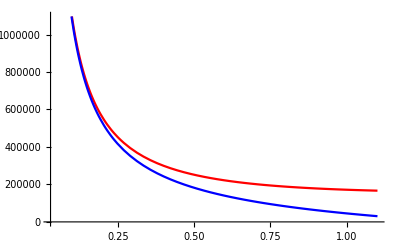

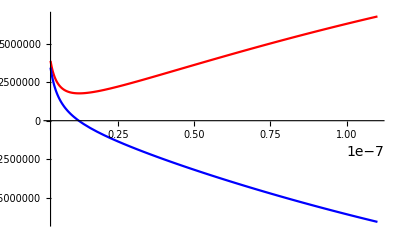

```mathematica
Plot[{potFuncCS[y]+esPot[y,2]+imagePot[2y,ϵ,q1],potFuncAS[y]-esPot[y,2]+imagePot[2y,ϵ,q1]},{y,0.1 σcs, rccs σcs},PlotStyle->{Red,Blue}]
Plot[{potFuncCS[y]+esPot[y,196]+imagePot[2y,ϵ,q1],potFuncAS[y]-esPot[y,196]+imagePot[2y,ϵ,q1]},{y,0.1 σcs,rccs σcs},PlotStyle->{Red,Blue}]
```

```mathematica
dxs=0.296 10^-7;
xp=0;zp=0;
forceTab={};
For[y=0.1dxs,y<=2.5dxs,y=y+0.01dxs,
totalpts=Length[bottomWall];
(*dist = Table[{grid[[ii]]-{0,y,0}},{ii,1,totalpts}];*)
absdist=Table[((bottomWall[[ii,1]]-xp)^2+(bottomWall[[ii,2]]-y)^2+(bottomWall[[ii,3]]-zp)^2)^(1/2),{ii,1,totalpts}];
force=Sum[lj126[absdist[[ii]],6.46 10^-12,dxs](y-bottomWall[[ii,2]])/absdist[[ii]],{ii,1,totalpts}];
AppendTo[forceTab,{y,force}];
];
forceFunc2=Interpolation[forceTab,InterpolationOrder->1];
```

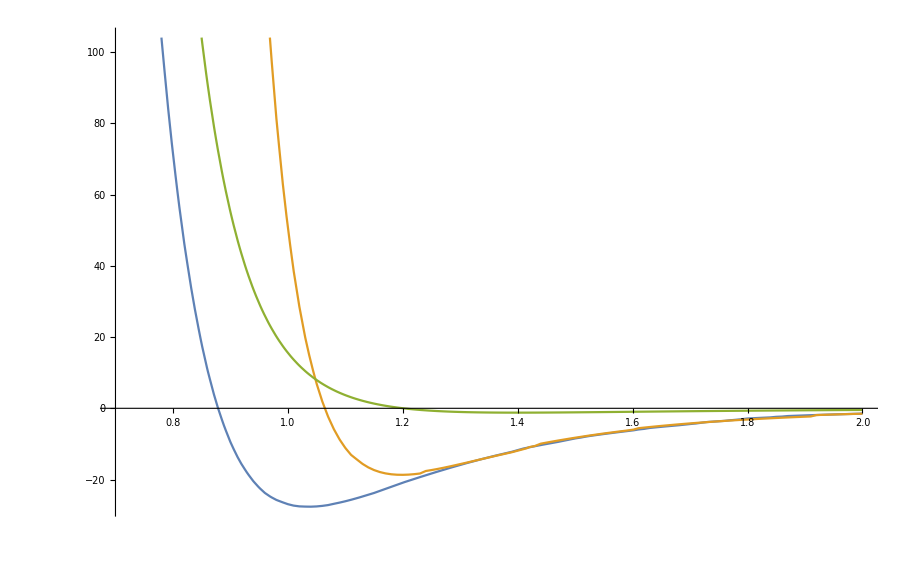

```mathematica
ljNew[r_,ξ_,σ_]= D[-4 ξ ((σ/r)^12-1.5(σ/r)^5),r];
Plot[{forceFunc[r dxs],forceFunc2[r dxs],lj93c[r,1,1]},{r,0.7,2}]
```

```mathematica
forceTab
```

{{0.01695,0.},{0.0339,0.},{0.05085,0.},{0.0678,0.},{0.08475,0.},{0.1017,0.},{0.11865,0.},{0.1356,0.},{0.15255,0.},{0.1695,0.},{0.18645,0.},{0.2034,0.},{0.22035,0.},{0.2373,0.},{0.25425,0.},{0.2712,0.},{0.28815,0.},{0.3051,0.},{0.32205,0.},{0.339,0.},{0.35595,0.},{0.3729,0.},{0.38985,0.},{0.4068,0.},{0.42375,0.},{0.4407,0.},{0.45765,0.},{0.4746,0.},{0.49155,0.},{0.5085,0.},{0.52545,0.},{0.5424,0.},{0.55935,0.},{0.5763,0.},{0.59325,0.},{0.6102,0.},{0.62715,0.},{0.6441,0.},{0.66105,0.},{0.678,0.},{0.69495,0.},{0.7119,0.},{0.72885,0.},{0.7458,0.},{0.76275,0.},{0.7797,0.},{0.79665,0.},{0.8136,0.},{0.83055,0.},{0.8475,0.}}

```mathematica
forceTab
```

```mathematica
Length[grid]
ListPointPlot3D[{grid},AspectRatio->1,AxesLabel->{"x","y","z"},BoxRatios->{1,0.1, 1}]
```

2793

-Graphics3D-

```mathematica
ptsXl=-21;
ptsXh=25;

ptsYl=-8;
ptsYh=33;

ptsZl=-8;
ptsZh=35;

dx=0.339;
rotY={{Cos[π/4],0,Sin[π/4]},{0,1,0},{-Sin[π/4],0,Cos[π/4]}};
rotX={{1,0,0},{0,Cos[0.9553166181245093],-Sin[0.9553166181245093]},{0,Sin[0.9553166181245093],Cos[0.9553166181245093]}};
grid1=Flatten[Table[{ii*dx,jj*dx,kk*dx},{ii,ptsXl,ptsXh},{jj,ptsYl,ptsYh},{kk,ptsZl,ptsZh}],2];
(*grid1={{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}};*)
grid=ParallelTable[rotX.rotY.grid1[[ii]],{ii,1,Length[grid1]}];
len=Length[grid]
For[i=1,i<=len,i++,
If[grid[[i,2]]>0.1dx,
grid =Delete[grid,i];
len--;
i--;
];
];
len=Length[grid];
For[i=1,i<=len,i++,
If[grid[[i,2]]<-2dx,
grid =Delete[grid,i];
len--;
i--;
];
];
len=Length[grid];
For[i=1,i<=len,i++,
If[grid[[i,1]]<-2 ||grid[[i,1]]>8 ||grid[[i,3]]<-2 ||grid[[i,3]]>8,
grid =Delete[grid,i];
len--;
i--;
];
];
```

86856

```mathematica
Export["~/bottomWall.dat",grid,"Table"]
```

~/bottomWall.dat

```mathematica
gridshift=Table[{grid[[ii,1]],grid[[ii,2]]-0.148,grid[[ii,3]]},{ii,1,Length[grid]}];
```

```mathematica
bottomWall = Table[{gridshift[[ii,1]]*10^-7,gridshift[[ii,2]]*10^-7,gridshift[[ii,3]]*10^-7},{ii,1,Length[grid]}];
topWall = Table[{bottomWall[[ii,1]],-bottomWall[[ii,2]]+6*10^-7,bottomWall[[ii,3]]},{ii,1,Length[grid]}];
ListPointPlot3D[{bottomWall,topWall},AspectRatio->1,AxesLabel->{"x","y","z"},BoxRatios->{8,9, 8}]
```

-Graphics3D-

```mathematica
bottomWallExp=Join[{Length[bottomWall]},bottomWall];
topWallExp=Join[{Length[topWall]},topWall];

Export["/home/drladiges/gigan/projects/FHDeX/exec/immersedIons/bottomWall.dat",bottomWallExp,"Table"];
Export["/home/drladiges/gigan/projects/FHDeX/exec/immersedIons/topWall.dat",topWallExp,"Table"];
```

```mathematica
Min[gridshift[[All,2]]]
```

-0.735165

```mathematica
(22.374/3-6)/2
```

0.729

```mathematica
list1=Select[grid,#[[2]]>-0.1&& #[[1]]>-0.1&& #[[1]]<6.1&& #[[3]]>-0.1&& #[[3]]<6.1 &];
Length[list1]
(*list2=Select[list1[[All,2]],#>-0.1&]*)
```

195

```mathematica
eps=(14.8 14.8)^(1/2);
Print["kilocal:"]
eps 4.184 10^10/(6.02 10^23)
Print["cal:"]
eps 4.184 10^10/(6.02 10^23)/1000
```

kilocal:

1.02862×10^-12

cal:

1.02862×10^-15

```mathematica
kb=1.38 10^-16;
T=298;
4kb T
```

1.64496×10^-13

```mathematica
8.16*10^-22*10^7
```

8.16×10^-15

```mathematica
0.5*10^7*10^3/(6.02 10^23)
```

8.30565×10^-15